# AOE Thin-Wall Project

Group 7 - Don’t call my name, Don’t call my name, Mariko. That’s not my name, That’s not my name, Thottman (Aesthetics), Vyon Coetzer, David Del Grosso, David Gardiner, Gaurav Sakhawala, Ronak Shah

```mathematica
ClearAll["Global`*"]
```

## Constants

```mathematica
ClearAll["Global`*"]
gfactor=1;
g=32.174*gfactor;(*gravity (ft/s2)*)
croot=38.94;(*chord at root (ft)*)
ctip=9.735;(*chord at tip (ft)*)
Wto=550000;(*take off weight (lbs)*)
Vcruise=490*1.68781;(*cruise velocity (ft/s)*)
Lw=95.8;(*wing lenght (ft)*)
Weng=10000;(*weight engine (lbs)*)
chordL[x_]=38.94+x*Tan[11.780589303200827 Degree]-x*Tan[35.61 Degree];
chordR[x_]=24.98+(x-27.5)*Tan[26.24608449458938 Degree]-(x-27.5)*Tan[35.61 Degree];

(*chord function of x to end*)
(*chord[x_]=Piecewise[{chordL[x],{0≤x<27.5}},{chordR[x],{27.5≤x≤95.8}}];
width[x_]=.65*chord[x];(*box breadth (ft)*)
height[x_]=0.05443575 chord[x];*)(*box height (ft)*)
heightL[x_]=.05443575*chordL[x];
widthL[x_]=.65*chordL[x];
heightR[x_]=.05443575*chordR[x];
widthR[x_]=.65*chordR[x];
(*widthL[x_]=0.65*chord[x];
heightL[x_]=0.05443575*chord[x];
widthR[x_]=0.65*chordR[x];
heightR[x_]=0.05443575*chordR[x];*)
e=.862;(*Oswald efficiency factor*)
cl=.3925;(*lift coef.at 3 AoA*)
cd=.0948;(*drag coef.at 3 AoA*)
Wlg=4320;(*weight landing gear (lbs)*)
Wfuel=.3*223378; (*fuel weight (lbs)*)
Llg=10.06; (*landing gear location (ft)*)
S=2062.4; (*wing area (ft2)*)
ρ=0.002377; (*air density (slug/ft3)*)
ρ35k=7.38*10^-4; (*air density (slug/ft3)*)
clmax=1.1263; (*max lift coefficient*)
ρAl=.1*12^3; (*density of aluminum (lb/ft3)*)
tcl[x_]=.01;
tcr[x_]=.01;
tL[x_]=tcl[x]*heightL[x];
tR[x_]=tcr[x]*heightR[x];
Wspar=Integrate[ρAl*widthL[x]*heightL[x]-ρAl*(widthL[x]-2tL[x])*(heightL[x]-2tL[x]),{x,0,27.5}]+Integrate[ρAl*widthR[x]*heightR[x]-ρAl*(widthR[x]-2tR[x])*(heightR[x]-2tR[x]),{x,27.5,95.8}];(*weight of spar (lbz)*)
AS=π*r^2;

ycL[x_]=heightL[x]/2;
ycR[x_]=heightR[x]/2;
zcL[x_]=widthL[x]/2;
zcR[x_]=widthR[x]/2;
IzzL[x_]=1/12 widthL[x] *heightL[x]^3-1/12*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])^3+4*AS*(ycL[x])^2;(*moment of inertia of lift(ft4)*)
IyyL[x_]=1/12 widthL[x]*heightL[x]^3-1/12*(heightL[x]-2tL[x])*(widthL[x]-2tL[x])^3+4*AS*(zcL[x])^2;


IzzR[x_]=1/12 widthR[x] *heightR[x]^3-1/12*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])^3+4*AS*(ycR[x])^2;(*moment of inertia of lift(ft4)*)
IyyR[x_]=1/12 widthR[x]*heightR[x]^3-1/12*(heightR[x]-2tR[x])*(widthR[x]-2tR[x])^3+4*AS*(zcR[x])^2;(*moment of inertia of drag (ft4)*)

Vstall=√(Wto/(1/2 ρ S clmax)); (*stall velocity (ft/s)*)
Vto=1.2 Vstall; (*takeoff velocity (ft/s)*)
AR=Lw^2/S; (*aspect ratio*)
EE=10.2*10^6*12^2; (*modulus of elasticity of Al 6061-T6 (psf)*)
T=90000; (*max thrust of engine (lbs)*)
FS=1.15; (*factor of safety*)
yieldstress=40000*12^2/FS; (*yield stress of wing (lb/ft2)*)
Rfuse=10.02; (*radius of fuselage (ft)*)
Ltaper=27.5;
```

## Case 1 (Takeoff)

Lift

```mathematica
(* distributed load *)
py[x_]=a x^2+b x+c;
Lift  = (1/2 )*ρ*Vto^2*S*clmax*e;
dpy[x_]=D[py[x],x];
eq1a=py[Lw]==0;
eq2a=dpy[0]==0;
eq3a=Integrate[py[x],{x,0,Lw}]==Lift/2;
sol1a=Solve[{eq1a,eq2a,eq3a},{a,b,c}];
a=a/.sol1a[[1]];
b=b/.sol1a[[1]];
c=c/.sol1a[[1]];
py[x_]=py[x];
Integrate[py[x],{x,0,Lw}]; (*total lift*)

PyWL[x_]=ρAl*widthL[x]*heightL[x]-ρAl*(widthL[x]-2tL[x])*(heightL[x]-2tL[x]);
PyWR[x_]=ρAl*widthR[x]*heightR[x]-ρAl*(widthR[x]-2tR[x])*(heightR[x]-2tR[x]);

VyL[x_]=Integrate[-(py[x]-Wfuel/Llg-PyWL[x]),x]+c1a;
VyLM[x_]=Integrate[-(py[x]-PyWL[x]),x]+c2a;
VyRM[x_]=Integrate[-(py[x]-PyWL[x]),x]+c3a;
VyR[x_]=Integrate[-(py[x]-PyWR[x]),x]+c4a;

MzL[x_]=Integrate[-VyL[x],x]+c5a;
MzLM[x_]=Integrate[-VyLM[x],x]+c6a;
MzRM[x_]=Integrate[-VyRM[x],x]+c7a;
MzR[x_]=Integrate[-VyR[x],x]+c8a;

rotyL[x_]=Integrate[MzL[x]/(EE IzzL[x]),x]+c9a;
rotyLM[x_]=Integrate[MzLM[x]/(EE IzzL[x]),x]+c10a;
rotyRM[x_]=Integrate[MzRM[x]/(EE IzzL[x]),x]+c11a;
rotyR[x_]=Integrate[MzR[x]/(EE IzzR[x]),x]+c12a;

uyL[x_]=Integrate[rotyL[x],x]+c13a;
uyLM[x_]=Integrate[rotyLM[x],x]+c14a;
uyRM[x_]=Integrate[rotyRM[x],x]+c15a;
uyR[x_]=Integrate[rotyR[x],x]+c16a;

(*boundary and matching conditions*)
eq4a=VyR[Lw]==0;
eq5a=MzR[Lw]==0;
eq6a=uyL[0]==0;
eq7a=rotyL[0]==0;
eq8a=rotyL[Llg]==rotyLM[Llg];
eq9a=rotyLM[Leng]==rotyRM[Leng];
eq10a=rotyRM[Ltaper]==rotyR[Ltaper];
eq11a=uyL[Llg]==uyLM[Llg];
eq12a=uyLM[Leng]==uyRM[Leng];
eq13a=uyRM[Ltaper]==uyR[Ltaper];
eq14a=MzL[Llg]==MzLM[Llg];
eq15a=MzLM[Leng]==MzRM[Leng];
eq16a=MzRM[Ltaper]==MzR[Ltaper];
eq17a=VyL[Llg]+Wlg==VyLM[Llg];
eq18a=VyLM[Leng]+Weng==VyRM[Leng];
eq19a=VyRM[Ltaper]== VyR[Ltaper];

sol2a=Solve[{eq4a,eq5a,eq6a,eq7a,eq8a,eq9a,eq10a,eq11a,eq12a,eq13a,eq14a,eq15a,eq16a,eq17a,eq18a,eq19a},{c1a,c2a,c3a,c4a,c5a,c6a,c7a,c8a,c9a,c10a,c11a,c12a,c13a,c14a,c15a,c16a}];

c1a=c1a/.sol2a[[1]];
c2a=c2a/.sol2a[[1]];
c3a=c3a/.sol2a[[1]];
c4a=c4a/.sol2a[[1]];
c5a=c5a/.sol2a[[1]];
c6a=c6a/.sol2a[[1]];
c7a=c7a/.sol2a[[1]];
c8a=c8a/.sol2a[[1]];
c9a=c9a/.sol2a[[1]];
c10a=c10a/.sol2a[[1]];
c11a=c11a/.sol2a[[1]];
c12a=c12a/.sol2a[[1]];
c13a=c13a/.sol2a[[1]];
c14a=c14a/.sol2a[[1]];
c15a=c15a/.sol2a[[1]];
c16a=c16a/.sol2a[[1]];

VyL[x_]=VyL[x];
VyLM[x_]=VyLM[x];
VyRM[x_]=VyRM[x];
VyR[x_]=VyR[x];
MzL[x_]=MzL[x];
MzLM[x_]=MzLM[x];
MzRM[x_]=MzRM[x];
MzR[x_]=MzR[x];
rotyL[x_]=rotyL[x];
rotyLM[x_]=rotyLM[x];
rotyRM[x_]=rotyRM[x];
rotyR[x_]=rotyR[x];
uyL[x_]=uyL[x];
uyLM[x_]=uyLM[x];
uyRM[x_]=uyRM[x];
uyR[x_]=uyR[x];
```

RootSum::pfn: System`TSolveDump`P$87680[1] is not a pure function.

General::stop: Further output of RootSum::pfn will be suppressed during this calculation.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Drag

```mathematica
pzL[x_]=-(1/2 ρ Vto^2 S cd)/Lw-py[x]^2/((1/2 ρ Vto^2 S π *e*AR)/Lw);
pzM[x_]=-(1/2 ρ Vto^2 S cd)/Lw-py[x]^2/((1/2 ρ Vto^2 S π *e*AR)/Lw);
pzR[x_]=-(1/2 ρ Vto^2 S cd)/Lw-py[x]^2/((1/2 ρ Vto^2 S π *e*AR)/Lw);

VzL[x_]=Integrate[-pzL[x],x]+c1b;
VzM[x_]=Integrate[-pzM[x],x]+c2b;
VzR[x_]=Integrate[-pzR[x],x]+c3b;

MyL[x_]=Integrate[VzL[x],x]+c4b;
MyM[x_]=Integrate[VzM[x],x]+c5b;
MyR[x_]=Integrate[VzR[x],x]+c6b;

rotzL[x_]=Integrate[-MyL[x]/(EE IyyL[x]),x]+c7b;
rotzM[x_]=Integrate[-MyM[x]/(EE IyyL[x]),x]+c8b;
rotzR[x_]=Integrate[-MyR[x]/(EE IyyR[x]),x]+c9b;

uzL[x_]=Integrate[rotzL[x],x]+c10b;
uzM[x_]=Integrate[rotzM[x],x]+c11b;
uzR[x_]=Integrate[rotzR[x],x]+c12b;

(*boundary and matching conditions*)
eq1b=VzR[Lw]==0;
eq2b=MyR[Lw]==0;
eq3b=rotzL[0]==0;
eq4b=uzL[0]==0;
eq5b=rotzL[Leng]==rotzM[Leng];
eq6b=rotzM[Ltaper]==rotzR[Ltaper];
eq7b=uzL[Leng]==uzM[Leng];
eq8b=uzM[Ltaper]==uzR[Ltaper];
eq9b=MyL[Leng]==MyM[Leng];
eq10b=MyM[Ltaper]==MyR[Ltaper];
eq11b=VzL[Leng]+T==VzM[Leng];
eq12b=VzM[Ltaper]==VzR[Leng];

(*solve for constants*)
sol1b=Solve[{eq1b,eq2b,eq3b,eq4b,eq5b,eq6b,eq7b,eq8b,eq9b,eq10b,eq11b,eq12b},{c1b,c2b,c3b,c4b,c5b,c6b,c7b,c8b,c9b,c10b,c11b,c12b}];
c1b=c1b/.sol1b[[1]];
c2b=c2b/.sol1b[[1]];
c3b=c3b/.sol1b[[1]];
c4b=c4b/.sol1b[[1]];
c5b=c5b/.sol1b[[1]];
c6b=c6b/.sol1b[[1]];
c7b=c7b/.sol1b[[1]];
c8b=c8b/.sol1b[[1]];
c9b=c9b/.sol1b[[1]];
c10b=c10b/.sol1b[[1]];
c11b=c11b/.sol1b[[1]];
c12b=c12b/.sol1b[[1]];

(*apply newfound constants*)
pzL[x_]=pzL[x];
pzM[x_]=pzM[x];
pzR[x_]=pzR[x];
VzL[x_]=VzL[x];
VzM[x_]=VzM[x];
VzR[x_]=VzR[x];
MyL[x_]=MyL[x];
MyM[x_]=MyM[x];
MyR[x_]=MyR[x];
rotzL[x_]=rotzL[x];
rotzM[x_]=rotzM[x];
rotzR[x_]=rotzR[x];
uzL[x_]=uzL[x];
uzM[x_]=uzM[x];
uzR[x_]=uzR[x];
```

Stress

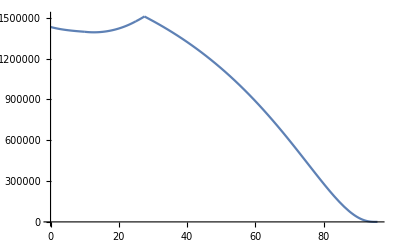

```mathematica
σxxL[x_,Leng_] =Abs[ (MyL[x]*-widthL[x]/2)/IyyL[x]]+Abs[(MzL[x]*heightL[x]/2)/IzzL[x]]; (*0 < x < 10.06 (Llg)*) 
σxxM1[x_,Leng_] = Abs[(MyL[x]*-widthL[x]/2)/IyyL[x]]+Abs[(MzLM[x]*heightL[x]/2)/IzzL[x]]; (*10.06 < x < Leng*)
σxxM2[x_,Leng_] = Abs[(MyM[x]*-widthL[x]/2)/IyyL[x]]+Abs[(MzRM[x]*heightL[x]/2)/IzzL[x]];(*Leng < x < 27.5*)
σxxR[x_,Leng_] = Abs[(MyR[x]*-widthR[x]/2)/IyyR[x]]+Abs[(MzR[x]*heightR[x]/2)/IzzR[x]];(*27.5 < x < 95.8*)
Leng=25;
plt1 = Plot[σxxL[x,Leng],{x,0,10.06}];
plt2 = Plot[σxxM1[x,Leng],{x,10.06,Leng}];
plt3 = Plot[σxxM2[x,Leng],{x,Leng,27.5}];
plt4 = Plot[σxxR[x,Leng],{x,27.5,95.8}];

Show[{plt1,plt2,plt3,plt4},PlotRange->All,AxesOrigin->{0,0}]
```

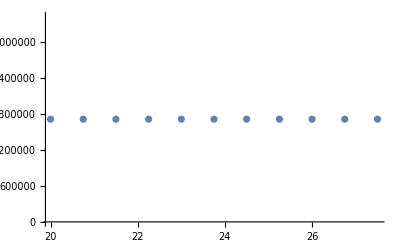

```mathematica
num=(27.5-20)/10;
uvec={};Do[AppendTo[uvec,σxxM2[27.5,Leng]],{Leng,20,27.5,num}]
data=Transpose@{Range[20,27.5,num],uvec};
ListPlot[data]
```

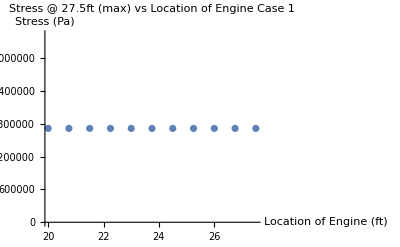

```mathematica
Show[%8935,AxesLabel->{HoldForm["Location of Engine (ft)"],HoldForm["Stress (Pa)"]},PlotLabel->HoldForm["Stress @ 27.5ft (max) vs Location of Engine Case 1"],LabelStyle->{GrayLevel[0]}]
```

```mathematica
num=(27.5-20)/10;
uvec={};Do[AppendTo[uvec,uyR[Lw]],{Leng,20,27.5,num}]
data=Transpose@{Range[20,27.5,num],uvec};
ListPlot[data];
```

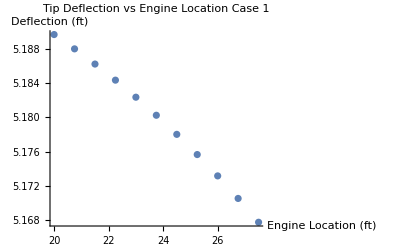

```mathematica
(*thick={height/4,height/8,height/12,height/15,height/20,height/25,height/50,height/100};
data1=Transpose@{thick,tipdeflection[Lw,20,thick]};
data2=Transpose@{thick,tipdeflection[Lw,(52.3+20)/2,thick]};
data3=Transpose@{thick,tipdeflection[Lw,52.3,thick]}*)
ListPlot[{data},PlotLabel->"Tip Deflection vs Engine Location Case 1",AxesLabel->{"Engine Location (ft)","Deflection (ft)"}]
```

```mathematica
t={height/4,height/8,height/20,height/50,height/100};
Leng=20;
dataL=Transpose@{t,σxx};
Leng=(52.3+20)/2;
dataM=Transpose@{t,σxx};
Leng=52.3;
dataR=Transpose@{t,σxx};
ListPlot[{dataL,dataM,dataR},PlotLegends->{"Leftmost Engine","Central Engine","Rightmost Engine"}]
```

Transpose::nmtx: The first two levels of {{height/4,height/8,height/20,height/50,height/100},-976874.} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.25 height,0.125 height,0.05 height,0.02 height,0.01 height},-976874.} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

-Graphics-

## Constants

```mathematica
ClearAll["Global`*"]
gfactor=1;
g=32.174*gfactor;(*gravity (ft/s2)*)
croot=38.94;(*chord at root (ft)*)
ctip=9.735;(*chord at tip (ft)*)
Wto=550000;(*take off weight (lbs)*)
Vcruise=490*1.68781;(*cruise velocity (ft/s)*)
Lw=95.8;(*wing lenght (ft)*)
Weng=10000;(*weight engine (lbs)*)
chordL[x_]=38.94+x*Tan[11.780589303200827 Degree]-x*Tan[35.61 Degree];
chordR[x_]=24.98+(x-27.5)*Tan[26.24608449458938 Degree]-(x-27.5)*Tan[35.61 Degree];
(*chord function of x to end*)
(*chord[x_]=Piecewise[{chordL[x],{0≤x<27.5}},{chordR[x],{27.5≤x≤95.8}}];
width[x_]=.65*chord[x];(*box breadth (ft)*)
height[x_]=0.05443575 chord[x];*)(*box height (ft)*)
heightL[x_]=.05443575*chordL[x];
widthL[x_]=.65*chordL[x];
heightR[x_]=.05443575*chordR[x];
widthR[x_]=.65*chordR[x];
(*widthL[x_]=0.65*chord[x];
heightL[x_]=0.05443575*chord[x];
widthR[x_]=0.65*chordR[x];
heightR[x_]=0.05443575*chordR[x];*)
e=.862;(*Oswald efficiency factor*)
cl=.3925;(*lift coef.at 3 AoA*)
cd=.0948;(*drag coef.at 3 AoA*)
Wlg=4320;(*weight landing gear (lbs)*)
Wfuel=.3*223378; (*fuel weight (lbs)*)
Llg=10.06; (*landing gear location (ft)*)
S=2062.4; (*wing area (ft2)*)
ρ=0.002377; (*air density (slug/ft3)*)
ρ35k=7.38*10^-4; (*air density (slug/ft3)*)
clmax=1.1263; (*max lift coefficient*)
ρAl=.1*12^3; (*density of aluminum (lb/ft3)*)

tL[x_]=.1*heightL[x];
tR[x_]=.1*heightR[x];
Wspar=Integrate[ρAl*widthL[x]*heightL[x]-ρAl*(widthL[x]-2tL[x])*(heightL[x]-2tL[x]),{x,0,27.5}]+Integrate[ρAl*widthR[x]*heightR[x]-ρAl*(widthR[x]-2tR[x])*(heightR[x]-2tR[x]),{x,27.5,95.8}];(*weight of spar (lbs)*)

IzzL[x_]=1/12 widthL[x] *heightL[x]^3-1/12*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])^3;(*moment of inertia of lift(ft4)*)
IyyL[x_]=1/12 widthL[x]*heightL[x]^3-1/12*(heightL[x]-2tL[x])*(widthL[x]-2tL[x])^3;


IzzR[x_]=1/12 widthR[x] *heightR[x]^3-1/12*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])^3;(*moment of inertia of lift(ft4)*)
IyyR[x_]=1/12 widthR[x]*heightR[x]^3-1/12*(heightR[x]-2tR[x])*(widthR[x]-2tR[x])^3;(*moment of inertia of drag (ft4)*)
Vstall=√(Wto/(1/2 ρ S clmax)); (*stall velocity (ft/s)*)
Vto=1.2 Vstall; (*takeoff velocity (ft/s)*)
AR=Lw^2/S; (*aspect ratio*)
EE=10.2*10^6*12^2; (*modulus of elasticity of Al 6061-T6 (psf)*)
T=90000; (*max thrust of engine (lbs)*)
FS=1.15; (*factor of safety*)
yieldstress=40000*12^2/FS; (*yield stress of wing (lb/ft2)*)
Rfuse=10.02; (*radius of fuselage (ft)*)
Ltaper=27.5;
```

## Case 2 (Engine Failure)

Lift

(0.000669296 (1.44426×10^12-5.64839×10^10 Leng+7.36345×10^8 Leng^2-3.19983×10^6 Leng^3+1. Leng^4))/(-76.7085+1. Leng)^3+1.71359 x+(0.0000174504 (-2.48627×10^11+9.72358×10^9 Leng-1.26751×10^8 Leng^2+550639. Leng^3+1. Leng^4) x)/(-76.7085+1. Leng)^3-0.00170736 x^2-18799.6/(-139.451+1. x)^2-3932.62/(-139.451+1. x)+428.242 Log[139.451-1. x]-1.71359 x Log[139.451-1. x]

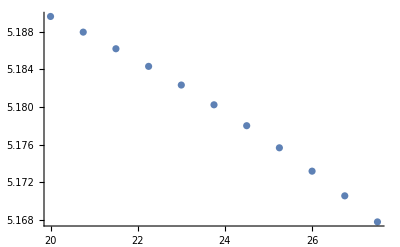

```mathematica
(* distributed load *)
py[x_]=a x^2+b x+c;
Lift  = (1/2 )*ρ*Vto^2*S*clmax*e;
dpy[x_]=D[py[x],x];
eq1a=py[Lw]==0;
eq2a=dpy[0]==0;
eq3a=Integrate[py[x],{x,0,Lw}]==Lift/2;
sol1a=Solve[{eq1a,eq2a,eq3a},{a,b,c}];
a=a/.sol1a[[1]];
b=b/.sol1a[[1]];
c=c/.sol1a[[1]];
py[x_]=py[x];
Integrate[py[x],{x,0,Lw}]; (*total lift*)

PyWL[x_]=ρAl*widthL[x]*heightL[x]-ρAl*(widthL[x]-2tL[x])*(heightL[x]-2tL[x]);
PyWR[x_]=ρAl*widthR[x]*heightR[x]-ρAl*(widthR[x]-2tR[x])*(heightR[x]-2tR[x]);

VyL[x_]=Integrate[-(py[x]-Wfuel/Llg-PyWL[x]),x]+c1a;
VyLM[x_]=Integrate[-(py[x]-PyWL[x]),x]+c2a;
VyRM[x_]=Integrate[-(py[x]-PyWL[x]),x]+c3a;
VyR[x_]=Integrate[-(py[x]-PyWR[x]),x]+c4a;

MzL[x_]=Integrate[-VyL[x],x]+c5a;
MzLM[x_]=Integrate[-VyLM[x],x]+c6a;
MzRM[x_]=Integrate[-VyRM[x],x]+c7a;
MzR[x_]=Integrate[-VyR[x],x]+c8a;

rotyL[x_]=Integrate[MzL[x]/(EE IzzL[x]),x]+c9a;
rotyLM[x_]=Integrate[MzLM[x]/(EE IzzL[x]),x]+c10a;
rotyRM[x_]=Integrate[MzRM[x]/(EE IzzL[x]),x]+c11a;
rotyR[x_]=Integrate[MzR[x]/(EE IzzR[x]),x]+c12a;

uyL[x_]=Integrate[rotyL[x],x]+c13a;
uyLM[x_]=Integrate[rotyLM[x],x]+c14a;
uyRM[x_]=Integrate[rotyRM[x],x]+c15a;
uyR[x_]=Integrate[rotyR[x],x]+c16a;

(*boundary and matching conditions*)
eq4a=VyR[Lw]==0;
eq5a=MzR[Lw]==0;
eq6a=uyL[0]==0;
eq7a=rotyL[0]==0;
eq8a=rotyL[Llg]==rotyLM[Llg];
eq9a=rotyLM[Leng]==rotyRM[Leng];
eq10a=rotyRM[Ltaper]==rotyR[Ltaper];
eq11a=uyL[Llg]==uyLM[Llg];
eq12a=uyLM[Leng]==uyRM[Leng];
eq13a=uyRM[Ltaper]==uyR[Ltaper];
eq14a=MzL[Llg]==MzLM[Llg];
eq15a=MzLM[Leng]==MzRM[Leng];
eq16a=MzRM[Ltaper]==MzR[Ltaper];
eq17a=VyL[Llg]+Wlg==VyLM[Llg];
eq18a=VyLM[Leng]+Weng==VyRM[Leng];
eq19a=VyRM[Ltaper]== VyR[Ltaper];

sol2a=Solve[{eq4a,eq5a,eq6a,eq7a,eq8a,eq9a,eq10a,eq11a,eq12a,eq13a,eq14a,eq15a,eq16a,eq17a,eq18a,eq19a},{c1a,c2a,c3a,c4a,c5a,c6a,c7a,c8a,c9a,c10a,c11a,c12a,c13a,c14a,c15a,c16a}];

c1a=c1a/.sol2a[[1]];
c2a=c2a/.sol2a[[1]];
c3a=c3a/.sol2a[[1]];
c4a=c4a/.sol2a[[1]];
c5a=c5a/.sol2a[[1]];
c6a=c6a/.sol2a[[1]];
c7a=c7a/.sol2a[[1]];
c8a=c8a/.sol2a[[1]];
c9a=c9a/.sol2a[[1]];
c10a=c10a/.sol2a[[1]];
c11a=c11a/.sol2a[[1]];
c12a=c12a/.sol2a[[1]];
c13a=c13a/.sol2a[[1]];
c14a=c14a/.sol2a[[1]];
c15a=c15a/.sol2a[[1]];
c16a=c16a/.sol2a[[1]];

VyL[x_]=VyL[x];
VyLM[x_]=VyLM[x];
VyRM[x_]=VyRM[x];
VyR[x_]=VyR[x];
MzL[x_]=MzL[x];
MzLM[x_]=MzLM[x];
MzRM[x_]=MzRM[x];
MzR[x_]=MzR[x];
rotyL[x_]=rotyL[x];
rotyLM[x_]=rotyLM[x];
rotyRM[x_]=rotyRM[x];
rotyR[x_]=rotyR[x];
uyL[x_]=uyL[x];
uyLM[x_]=uyLM[x];
uyRM[x_]=uyRM[x];
uyR[x_]=uyR[x]



num=(27.5-20)/10;
uvec={};Do[AppendTo[uvec,uyR[Lw]],{Leng,20,27.5,num}]
data=Transpose@{Range[20,27.5,num],uvec};
ListPlot[data]
```

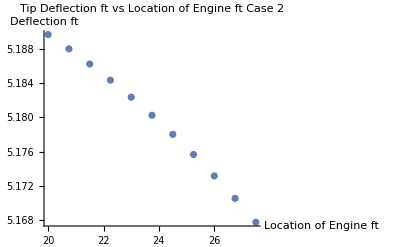

```mathematica
Show[%8017,AxesLabel->{HoldForm[Location of Engine ft],HoldForm[Deflection ft]},PlotLabel->HoldForm[Tip Deflection ft vs Location of Engine ft Case 2],LabelStyle->{GrayLevel[0]}]
```

Drag

```mathematica
pzL[x_]=-(1/2 ρ35k Vcruise^2 S cd)/Lw-py[x]^2/((1/2 ρ35k Vcruise^2 S π *e*AR)/Lw);
pzM[x_]=-(1/2 ρ35k Vcruise^2 S cd)/Lw-py[x]^2/((1/2 ρ35k Vcruise^2 S π *e*AR)/Lw);
pzR[x_]=-(1/2 ρ35k Vcruise^2 S cd)/Lw-py[x]^2/((1/2 ρ35k Vcruise^2 S π *e*AR)/Lw);

VzL[x_]=Integrate[-pzL[x],x]+c1b;
VzM[x_]=Integrate[-pzM[x],x]+c2b;
VzR[x_]=Integrate[-pzR[x],x]+c3b;

MyL[x_]=Integrate[VzL[x],x]+c4b;
MyM[x_]=Integrate[VzM[x],x]+c5b;
MyR[x_]=Integrate[VzR[x],x]+c6b;

rotzL[x_]=Integrate[-MyL[x]/(EE IyyL[x]),x]+c7b;
rotzM[x_]=Integrate[-MyM[x]/(EE IyyL[x]),x]+c8b;
rotzR[x_]=Integrate[-MyR[x]/(EE IyyR[x]),x]+c9b;

uzL[x_]=Integrate[rotzL[x],x]+c10b;
uzM[x_]=Integrate[rotzM[x],x]+c11b;
uzR[x_]=Integrate[rotzR[x],x]+c12b;

(*boundary and matching conditions*)
eq1b=VzR[Lw]==0;
eq2b=MyR[Lw]==0;
eq3b=rotzL[0]==0;
eq4b=uzL[0]==0;
eq5b=rotzL[Leng]==rotzM[Leng];
eq6b=rotzM[Ltaper]==rotzR[Ltaper];
eq7b=uzL[Leng]==uzM[Leng];
eq8b=uzM[Ltaper]==uzR[Ltaper];
eq9b=MyL[Leng]==MyM[Leng];
eq10b=MyM[Ltaper]==MyR[Ltaper];
eq11b=VzL[Leng]+T==VzM[Leng];
eq12b=VzM[Ltaper]==VzR[Leng];

(*solve for constants*)
sol1b=Solve[{eq1b,eq2b,eq3b,eq4b,eq5b,eq6b,eq7b,eq8b,eq9b,eq10b,eq11b,eq12b},{c1b,c2b,c3b,c4b,c5b,c6b,c7b,c8b,c9b,c10b,c11b,c12b}];
c1b=c1b/.sol1b[[1]];
c2b=c2b/.sol1b[[1]];
c3b=c3b/.sol1b[[1]];
c4b=c4b/.sol1b[[1]];
c5b=c5b/.sol1b[[1]];
c6b=c6b/.sol1b[[1]];
c7b=c7b/.sol1b[[1]];
c8b=c8b/.sol1b[[1]];
c9b=c9b/.sol1b[[1]];
c10b=c10b/.sol1b[[1]];
c11b=c11b/.sol1b[[1]];
c12b=c12b/.sol1b[[1]];

(*apply newfound constants*)
pzL[x_]=pzL[x];
pzM[x_]=pzM[x];
pzR[x_]=pzR[x];
VzL[x_]=VzL[x];
VzM[x_]=VzM[x];
VzR[x_]=VzR[x];
MyL[x_]=MyL[x];
MyM[x_]=MyM[x];
MyR[x_]=MyR[x];
rotzL[x_]=rotzL[x];
rotzM[x_]=rotzM[x];
rotzR[x_]=rotzR[x];
uzL[x_]=uzL[x];
uzM[x_]=uzM[x];
uzR[x_]=uzR[x];
```

Stress

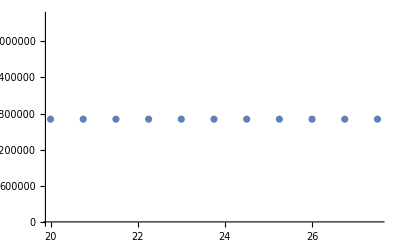

```mathematica
σxxL[x_,Leng_] =Abs[ (MyL[x]*-widthL[x]/2)/IyyL[x]]+Abs[(MzL[x]*heightL[x]/2)/IzzL[x]]; (*0 < x < 10.06 (Llg)*) 
σxxM1[x_,Leng_] = Abs[(MyL[x]*-widthL[x]/2)/IyyL[x]]+Abs[(MzLM[x]*heightL[x]/2)/IzzL[x]]; (*10.06 < x < Leng*)
σxxM2[x_,Leng_] = Abs[(MyM[x]*-widthL[x]/2)/IyyL[x]]+Abs[(MzRM[x]*heightL[x]/2)/IzzL[x]];(*Leng < x < 27.5*)
σxxR[x_,Leng_] = Abs[(MyR[x]*-widthR[x]/2)/IyyR[x]]+Abs[(MzR[x]*heightR[x]/2)/IzzR[x]];(*27.5 < x < 95.8*)

(*plt1 = Plot[σxxL[x,Leng],{x,0,10.06}];
plt2 = Plot[σxxM1[x,Leng],{x,10.06,Leng}];
plt3 = Plot[σxxM2[x,Leng],{x,Leng,27.5}];
plt4 = Plot[σxxR[x,Leng],{x,27.5,95.8}];

Show[{plt1,plt2,plt3,plt4},PlotRange->All,AxesOrigin->{0,0}];*)

num=(27.5-20)/10;
uvec={};Do[AppendTo[uvec,σxxM2[27.5,Leng]],{Leng,20,27.5,num}]
data=Transpose@{Range[20,27.5,num],uvec};
ListPlot[data]
```

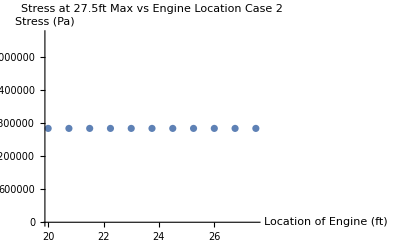

```mathematica
Show[%8086,AxesLabel->{HoldForm["Location of Engine (ft)"],HoldForm["Stress (Pa)"]},PlotLabel->HoldForm["Stress at 27.5ft Max vs Engine Location Case 2"],LabelStyle->{GrayLevel[0]}]
```

```mathematica
maxLeng=Solve[T*(Leng+Rfuse)== 5390000/FS,Leng];
maxLeng=Leng/.maxLeng[[1]]
```

42.0573

## Constants

```mathematica
ClearAll["Global`*"]
gfactor=1;
g=32.174*gfactor;(*gravity (ft/s2)*)
croot=38.94;(*chord at root (ft)*)
ctip=9.735;(*chord at tip (ft)*)
Wto=550000;(*take off weight (lbs)*)
Vcruise=490*1.68781;(*cruise velocity (ft/s)*)
Lw=95.8;(*wing lenght (ft)*)
Weng=10000;(*weight engine (lbs)*)
chordL[x_]=38.94+x*Tan[11.780589303200827 Degree]-x*Tan[35.61 Degree];
chordR[x_]=24.98+(x-27.5)*Tan[26.24608449458938 Degree]-(x-27.5)*Tan[35.61 Degree];
(*chord function of x to end*)
(*chord[x_]=Piecewise[{chordL[x],{0≤x<27.5}},{chordR[x],{27.5≤x≤95.8}}];
width[x_]=.65*chord[x];(*box breadth (ft)*)
height[x_]=0.05443575 chord[x];*)(*box height (ft)*)
heightL[x_]=.05443575*chordL[x];
widthL[x_]=.65*chordL[x];
heightR[x_]=.05443575*chordR[x];
widthR[x_]=.65*chordR[x];
(*widthL[x_]=0.65*chord[x];
heightL[x_]=0.05443575*chord[x];
widthR[x_]=0.65*chordR[x];
heightR[x_]=0.05443575*chordR[x];*)
e=.862;(*Oswald efficiency factor*)
cl=.3925;(*lift coef.at 3 AoA*)
cd=.0948;(*drag coef.at 3 AoA*)
Wlg=4320;(*weight landing gear (lbs)*)
Wfuel=.3*223378; (*fuel weight (lbs)*)
Llg=10.06; (*landing gear location (ft)*)
S=2062.4; (*wing area (ft2)*)
ρ=0.002377; (*air density (slug/ft3)*)
ρ35k=7.38*10^-4; (*air density (slug/ft3)*)
clmax=1.1263; (*max lift coefficient*)
ρAl=.1*12^3; (*density of aluminum (lb/ft3)*)

tL[x_]=.1*heightL[x];
tR[x_]=.1*heightR[x];
Wspar=Integrate[ρAl*widthL[x]*heightL[x]-ρAl*(widthL[x]-2tL[x])*(heightL[x]-2tL[x]),{x,0,27.5}]+Integrate[ρAl*widthR[x]*heightR[x]-ρAl*(widthR[x]-2tR[x])*(heightR[x]-2tR[x]),{x,27.5,95.8}];(*weight of spar (lbs)*)

IzzL[x_]=1/12 widthL[x] *heightL[x]^3-1/12*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])^3;(*moment of inertia of lift(ft4)*)
IyyL[x_]=1/12 widthL[x]*heightL[x]^3-1/12*(heightL[x]-2tL[x])*(widthL[x]-2tL[x])^3;


IzzR[x_]=1/12 widthR[x] *heightR[x]^3-1/12*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])^3;(*moment of inertia of lift(ft4)*)
IyyR[x_]=1/12 widthR[x]*heightR[x]^3-1/12*(heightR[x]-2tR[x])*(widthR[x]-2tR[x])^3;(*moment of inertia of drag (ft4)*)
Vstall=√(Wto/(1/2 ρ S clmax)); (*stall velocity (ft/s)*)
Vto=1.2 Vstall; (*takeoff velocity (ft/s)*)
AR=Lw^2/S; (*aspect ratio*)
EE=10.2*10^6*12^2; (*modulus of elasticity of Al 6061-T6 (psf)*)
T=90000; (*max thrust of engine (lbs)*)
FS=1.15; (*factor of safety*)
yieldstress=40000*12^2/FS; (*yield stress of wing (lb/ft2)*)
Rfuse=10.02; (*radius of fuselage (ft)*)
Ltaper=27.5;
```

65815.

## Case 3 (Static)

```mathematica
a=17.58; b=22.85; c=53.27; d=74.63;
 e=93.18; f=118.32; g=144.42; h=156.11;
sol3a=Solve[0== -Wto*(67)+2*Flg*(e-a),Flg]
Flg=Flg/.sol3a[[1]];
```

{{Flg→243717.}}

(0.000669296 (2.77382×10^8-1.08482×10^7 Leng+141421. Leng^2-691.247 Leng^3+1. Leng^4))/(-76.7085+1. Leng)^3-3.89585×10^-17 x+(0.0000174504 (-3.83266×10^7+1.49892×10^6 Leng-10714.2 Leng^2-106.859 Leng^3+1. Leng^4) x)/(-76.7085+1. Leng)^3-0.000171341 x^2-622.072/(-139.451+1. x)^2-57.0041/(-139.451+1. x)-1.54062×10^-14 Log[139.451-1. x]+3.89585×10^-17 x Log[139.451-1. x]

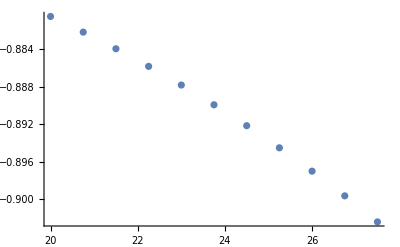

```mathematica
(* distributed load *)
py[x_]=0;
PyWL[x_]=ρAl*widthL[x]*heightL[x]-ρAl*(widthL[x]-2tL[x])*(heightL[x]-2tL[x]);
PyWR[x_]=ρAl*widthR[x]*heightR[x]-ρAl*(widthR[x]-2tR[x])*(heightR[x]-2tR[x]);

VyL[x_]=Integrate[-(py[x]-Wfuel/Llg-PyWL[x]),x]+c1a;
VyLM[x_]=Integrate[-(py[x]-PyWL[x]),x]+c2a;
VyRM[x_]=Integrate[-(py[x]-PyWL[x]),x]+c3a;
VyR[x_]=Integrate[-(py[x]-PyWR[x]),x]+c4a;

MzL[x_]=Integrate[-VyL[x],x]+c5a;
MzLM[x_]=Integrate[-VyLM[x],x]+c6a;
MzRM[x_]=Integrate[-VyRM[x],x]+c7a;
MzR[x_]=Integrate[-VyR[x],x]+c8a;

rotyL[x_]=Integrate[MzL[x]/(EE IzzL[x]),x]+c9a;
rotyLM[x_]=Integrate[MzLM[x]/(EE IzzL[x]),x]+c10a;
rotyRM[x_]=Integrate[MzRM[x]/(EE IzzL[x]),x]+c11a;
rotyR[x_]=Integrate[MzR[x]/(EE IzzR[x]),x]+c12a;

uyL[x_]=Integrate[rotyL[x],x]+c13a;
uyLM[x_]=Integrate[rotyLM[x],x]+c14a;
uyRM[x_]=Integrate[rotyRM[x],x]+c15a;
uyR[x_]=Integrate[rotyR[x],x]+c16a;

(*boundary and matching conditions*)
eq4a=VyR[Lw]==0;
eq5a=MzR[Lw]==0;
eq6a=uyL[0]==0;
eq7a=rotyL[0]==0;
eq8a=rotyL[Llg]==rotyLM[Llg];
eq9a=rotyLM[Leng]==rotyRM[Leng];
eq10a=rotyRM[Ltaper]==rotyR[Ltaper];
eq11a=uyL[Llg]==uyLM[Llg];
eq12a=uyLM[Leng]==uyRM[Leng];
eq13a=uyRM[Ltaper]==uyR[Ltaper];
eq14a=MzL[Llg]==MzLM[Llg];
eq15a=MzLM[Leng]==MzRM[Leng];
eq16a=MzRM[Ltaper]==MzR[Ltaper];
eq17a=VyL[Llg]+Wlg==VyLM[Llg]+Flg;
eq18a=VyLM[Leng]+Weng==VyRM[Leng];
eq19a=VyRM[Ltaper]== VyR[Ltaper];

sol2a=Solve[{eq4a,eq5a,eq6a,eq7a,eq8a,eq9a,eq10a,eq11a,eq12a,eq13a,eq14a,eq15a,eq16a,eq17a,eq18a,eq19a},{c1a,c2a,c3a,c4a,c5a,c6a,c7a,c8a,c9a,c10a,c11a,c12a,c13a,c14a,c15a,c16a}];

c1a=c1a/.sol2a[[1]];
c2a=c2a/.sol2a[[1]];
c3a=c3a/.sol2a[[1]];
c4a=c4a/.sol2a[[1]];
c5a=c5a/.sol2a[[1]];
c6a=c6a/.sol2a[[1]];
c7a=c7a/.sol2a[[1]];
c8a=c8a/.sol2a[[1]];
c9a=c9a/.sol2a[[1]];
c10a=c10a/.sol2a[[1]];
c11a=c11a/.sol2a[[1]];
c12a=c12a/.sol2a[[1]];
c13a=c13a/.sol2a[[1]];
c14a=c14a/.sol2a[[1]];
c15a=c15a/.sol2a[[1]];
c16a=c16a/.sol2a[[1]];

VyL[x_]=VyL[x];
VyLM[x_]=VyLM[x];
VyRM[x_]=VyRM[x];
VyR[x_]=VyR[x];
MzL[x_]=MzL[x];
MzLM[x_]=MzLM[x];
MzRM[x_]=MzRM[x];
MzR[x_]=MzR[x];
rotyL[x_]=rotyL[x];
rotyLM[x_]=rotyLM[x];
rotyRM[x_]=rotyRM[x];
rotyR[x_]=rotyR[x];
uyL[x_]=uyL[x];
uyLM[x_]=uyLM[x];
uyRM[x_]=uyRM[x];
uyR[x_]=uyR[x]

num=(27.5-20)/10;
(*uvec={};Do[AppendTo[uvec,uyR[Leng]],{Leng,20,27.5,num}]
data1=Transpose@{Range[20,27.5,num],uvec};
ListPlot[data1] (*deflection at Leng*);*)


uvec2={};Do[AppendTo[uvec2,uyR[Lw]],{Leng,20,27.5,num}];
data2=Transpose@{Range[20,27.5,num],uvec2};
ListPlot[data2] (*deflection at Lw*)





(*thick={height/4,height/8,height/12,height/15,height/20,height/25,height/50,height/100};
data1=Transpose@{thick,tipdeflection[Lw,20,thick]}
data2=Transpose@{thick,tipdeflection[Lw,(52.3+20)/2,thick]};
data3=Transpose@{thick,tipdeflection[Lw,52.3,thick]};
ListPlot[{data1,data2,data3},PlotLegends->{"Leftmost Engine","Central Engine","Rightmost Engine"},PlotLabel->"Tip Deflection",AxesLabel->{"Thickness (ft)","Deflection (ft)"}]*)
```

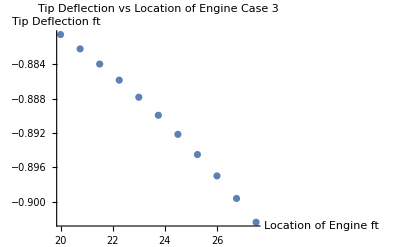

```mathematica
Show[%8772,AxesLabel->{HoldForm[Location of Engine ft],HoldForm[Tip Deflection ft]},PlotLabel->HoldForm[Tip Deflection vs Location of Engine Case 3],LabelStyle->{GrayLevel[0]}]
```

```mathematica
{{0.13248300656249998,-23.08462321638492},{0.06624150328124999,-11.603174462498314},{0.021197281049999996,11.884766836036333},{0.010598640524999998,41.998900299869774},{0.005299320262499999,101.14113311866477}}
```

{{0.132483,-23.0846},{0.0662415,-11.6032},{0.0211973,11.8848},{0.0105986,41.9989},{0.00529932,101.141}}

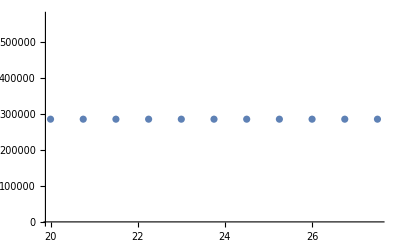

```mathematica
σxxL[x_,Leng_] =Abs[(MzL[x]*heightL[x]/2)/IzzL[x]]; (*0 < x < 10.06 (Llg)*) 
σxxM1[x_,Leng_] =Abs[(MzLM[x]*heightL[x]/2)/IzzL[x]]; (*10.06 < x < Leng*)
σxxM2[x_,Leng_] = Abs[(MzRM[x]*heightL[x]/2)/IzzL[x]];(*Leng < x < 27.5*)
σxxR[x_,Leng_] = Abs[(MzR[x]*heightR[x]/2)/IzzR[x]];(*27.5 < x < 95.8*)


num=(27.5-20)/10;
uvec3={};Do[AppendTo[uvec3,Abs[σxxM2[27.5,Leng]]],{Leng,20,27.5,num}]
data=Transpose@{Range[20,27.5,num],uvec3};
ListPlot[data]
```

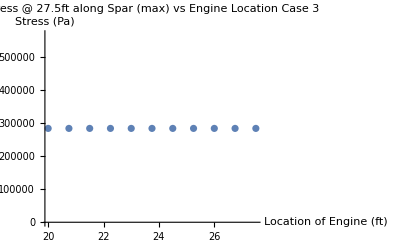

```mathematica
Show[%8776,AxesLabel->{HoldForm["Location of Engine (ft)"],HoldForm["Stress (Pa)"]},PlotLabel->HoldForm["Stress @ 27.5ft along Spar (max) vs Engine Location Case 3"],LabelStyle->{GrayLevel[0]}]
```